# isochronous pendulum

```mathematica
(* cycloid *)
{ θ-Sin[θ],1-Cos[θ]}
```

```mathematica
(* the inverted cycloid is *)
{ θ-Sin[θ],Cos[θ]-1}
```

```mathematica
Manipulate[
Show[
ParametricPlot[
{{θ-Sin[θ],Cos[θ]-1},{Cos[θ]+ϕ,Sin[θ]-1}},{θ,0,2π}],
ListPlot[{{ϕ,0},{ϕ,-1},{ϕ-Sin[ϕ],Cos[ϕ]-1}},Joined->True]
],{ϕ,0,2π}]
```

```mathematica
(* Now, a in-elastic string with length l, hanging at the origin *)
(* Prove that the period of this pendulum is independent of the amplitude *)
```

```mathematica
(* the arc lenght of the cycloid is *)
Integrate[√((1-Cos[θ])^2+(-Sin[θ])^2),{θ,0,ϕ},Assumptions->0<ϕ<2π ]
```

8 Sin[ϕ/4]^2

```mathematica
s[ϕ_]:=8 Sin[ϕ/4]^2
Table[s[ϕ],{ϕ,0,2π,π/2}]
```

{0,8 Sin[π/8]^2,4,8 Cos[π/8]^2,8}

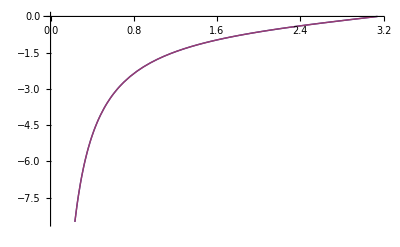

```mathematica
(* the Slope of the cycloid is *)
Plot[{(-Sin[θ])/(1-Cos[θ]),-Cot[θ/2]},{θ,0,π}]
```

```mathematica
(* When the string make a angle α with verticle, The length that touched with the cycloid is *)
Solve[Cot[α]==Sin[ϕ]/(1-Cos[ϕ]),ϕ]
```

Solve::verif: Potential solution {ϕ → 0} (possibly discarded by verifier) should be checked by hand. May require use of limits.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕ→2 α}}

```mathematica
(* That means, for given α, ϕ = 2 α *)
```

```mathematica
(* the length cover by the cycloid is *)
d[α_]:=8 Sin[α/2]^2
Table[d[α],{α,0,π/2,π/4}]
```

{0,8 Sin[π/8]^2,4}

```mathematica
(* the locus of the end of the string is *)
{x,y}=Simplify[{2α-Sin[2α]+(l - 8 Sin[α/2]^2)Sin[α],Cos[2α]-1 -(l - 8 Sin[α/2]^2)Cos[α]},Assumptions->0<α<π/2]
```

{2 α+(-4+l) Sin[α]+Sin[2 α],-3-(-4+l) Cos[α]-Cos[2 α]}

```mathematica
Manipulate[
Show[
ParametricPlot[
{{2α +Sin[2α]+ (l - 4)Sin[α], -3-Cos[2α]+Cos[α] (4-l)},
{ 2α-Sin[2α],Cos[2α]-1}},{α,-π/2,π/2}],
ListPlot[{{2θ-Sin[2θ],-3},{ 2θ-Sin[2θ],Cos[2θ]-1},{2θ +Sin[2θ]+ (l - 4)Sin[θ], -3-Cos[2θ]+Cos[θ] (4-l)}},Joined->True,PlotStyle->Green],
ParametricPlot[
{{Cos[α]+2θ,Sin[α]-1},{Cos[α]+2θ,Sin[α]-3}},{α,0,2π}],
ListPlot[{{2θ,0},{2θ,-1},{2θ-Sin[2θ],Cos[2θ]-1}},Joined->True],
ListPlot[{{2θ,-2},{2θ,-3},{2θ +Sin[2θ]+ (l - 4)Sin[θ], -3-Cos[2θ]+Cos[θ] (4-l)}},Joined->True]
]
,{{l,4},0,5},{θ,-π/2,π/2}]
```

```mathematica
(* The K.E. is *)
v^2=((ⅆ x)/(ⅆ t))^2+((ⅆ y)/(ⅆ t))^2
=(((ⅆ x)/(ⅆ α))^2+((ⅆ y)/(ⅆ α))^2)((ⅆ α)/(ⅆ t))^2
```

```mathematica
Simplify[D[x,α]^2+D[y,α]^2,Assumptions-> α ϵ Real]
```

(-4+l+4 Cos[α])^2

```mathematica
(* The potential energy should proportional to the height *)
Manipulate[Plot[ -3-Cos[2α]+Cos[α] (4-l),{α,0,π/2},PlotRange->{-4,0}],{{l,4},0,4}]
```

```mathematica
(* The Langrangian of the particle with angle α *)
L[α,α']=1/2 m (x'[α]^2+y'[α]^2) (α')^2-m g y[α]
```

```mathematica
L=1/2 m(-4+l+4 Cos[α[t]])^2 α'[t]^2-m g (-3-(-4+l) Cos[α[t]]-Cos[2 α[t]]);
Simplify[D[D[L,α'[t]],t]==D[L,α[t]],Assumptions->0<α<π/2]
```

m (-4+l+4 Cos[α[t]]) (g Sin[α[t]]-4 Sin[α[t]] α'[t]^2+(-4+l+4 Cos[α[t]]) α''[t])==0

```mathematica
DSolve[g Sin[α[t]]-4 Sin[α[t]] α'[t]^2+(4 Cos[α[t]]) α''[t]==0,α[t],t]
```

```mathematica
(* Langragian in arc length on the cycliod *)
L[arc,arc']=1/2 m arc'[t]^2-m g y[arc[t]]
```

```mathematica
d[α]
y
```

8 Sin[α/2]^2

-3-(-4+l) Cos[α]-Cos[2 α]

```mathematica
-3-(-4+l) Cos[α]-Cos[2 α]/.Cos[2α]->2 Cos[α]^2-1/.Cos[α]->1-Arc[t]/4//Simplify
```

1/8 (-8 l+2 l Arc[t]-Arc[t]^2)

```mathematica
Manipulate[Plot[1/8 (-8 l+2 l Arc-Arc^2),{Arc,0,4}],{l,0,4}]
```

```mathematica
L=1/2 m arc'[t]^2-m g (1/8 (-8 l+2 l arc[t]-arc[t]^2))
Simplify[D[D[L,arc'[t]],t]==D[L,arc[t]],Assumptions->0<arc[t]<l]
```

-1/8 g m (-8 l+2 l arc[t]-arc[t]^2)+1/2 m arc'[t]^2

m (g l+4 arc''[t])==g m arc[t]

```mathematica
DSolve[{m (g l+4 arc''[t])==g m arc[t],arc[0]==k,arc'[0]==0},arc[t],t]//ExpToTrig//Simplify
```

{{arc[t]→l+(k-l) Cosh[(√g t)/2]}}

```mathematica
arc[t]=l+(k-l)Cosh[(√g)/2 t]
(* we can see the time is not depend on k *)
arc[t] = 8 Sin[α/2]^2(* α is the angle with vertical *)
l+(k-l)Cosh[(√g)/2 t]==8 Sin[α/2]^2
(* set β is the angle on the pendulum cycliod *)
β = π - 2α
α = (π-β)/2
```

```mathematica
Manipulate[
Plot[l+(k-l)Cosh[(√g)/2 t],{t,0,20},PlotRange-> 4],{{l,4},0,4},{k,0,l},{g,1,2}]
```

```mathematica
(* Suppose the string l = 4  *)
```

```mathematica
x4=x/.l->4
y4=y/.l->4
```

2 α+Sin[2 α]

-3-Cos[2 α]

```mathematica
(* let the angle is θ, initailly *)
(* The conervation of energy *)
1/2(D[x4,α]^2+D[y4,α]^2)(α')^2-(3+Cos[2α])g==-(3+Cos[2θ])g//Simplify
```

g (Cos[2 α]-Cos[2 θ])==8 Cos[α]^2 (α')^2

```mathematica
Integrate[Cos[α]/(√(Cos[2 α]-Cos[2 θ])),α]
```

ArcTan[(√2 Sin[α])/(√(Cos[2 α]-Cos[2 θ]))]/(√2)

```mathematica
ArcTan[∞]-ArcTan[0]
```

π/2

```mathematica
Manipulate[Plot[Cos[α]/(√(Cos[2 α]-Cos[2 θ])),{α,0,π/2},PlotRange->2],{θ,0,π/2}]
```

```mathematica
(* for noraml pendulum*)
1/2 m l^2 (α')^2-l Cos[α]m g = -Cos[θ] l m g
 (α')^2= (2m g)/l(Cos[α]-Cos[θ])
```

```mathematica
Lnorm = 1/2 m l^2 (α'[t])^2-l Cos[α[t]]m g 
Simplify[D[D[Lnorm,α'[t]],t]==D[Lnorm,α[t]]]
```

-g l m Cos[α[t]]+1/2 l^2 m α'[t]^2

l^2 m α''[t]==g l m Sin[α[t]]

```mathematica
DSolve[l^2 m α''[t]==g l m Sin[α[t]],α[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{α[t]→-2 JacobiAmplitude[(√(-2 g t^2+l t^2 C[1]-4 g t C[2]+2 l t C[1] C[2]-2 g C[2]^2+l C[1] C[2]^2))/(2 √l),(4 g)/(2 g-l C[1])]},{α[t]→2 JacobiAmplitude[(√(-2 g t^2+l t^2 C[1]-4 g t C[2]+2 l t C[1] C[2]-2 g C[2]^2+l C[1] C[2]^2))/(2 √l),(4 g)/(2 g-l C[1])]}}